```mathematica
Naloga 1
```

```mathematica
T = Trikotnik[{0,0},{5,1},{7,4}]
```

Trikotnik[{0,0},{5,1},{7,4}]

```mathematica
Stranice[Trikotnik[{AA_,BB_,CC_}]] := {Daljica[AA,BB], Daljica[BB, CC], Daljica[CC,AA]}
```

```mathematica
Stranice[{{0,0}, {5,1}, {7,4}}]
```

{Daljica[{0,0},{5,1}],Daljica[{5,1},{7,4}],Daljica[{7,4},{0,0}]}

```mathematica
Koti[Trikotnik[AA_, BB_, CC_]] = {Kot[CC, AA, BB], Kot[AA, BB, CC], Kot[BB, CC, AA]}
```

{Kot[CC,AA,BB],Kot[AA,BB,CC],Kot[BB,CC,AA]}

```mathematica
Koti[Trikotnik[{0,0}, {5,1}, {7,4}]]
```

{Kot[{7,4},{0,0},{5,1}],Kot[{0,0},{5,1},{7,4}],Kot[{5,1},{7,4},{0,0}]}

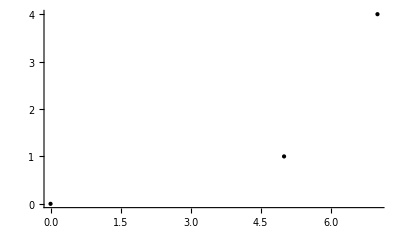

```mathematica
Graphics[{Point[{0,0}], Point[{5,1}], Point[{7,4}]}, Axes -> True]
```

```mathematica
SlikaOglisc[Trikotnik[AA_,BB_,CC_]]:= Graphics[{Point[AA], Point[BB], Point[CC]}]
SlikaOglisc[T]
```

-Graphics-

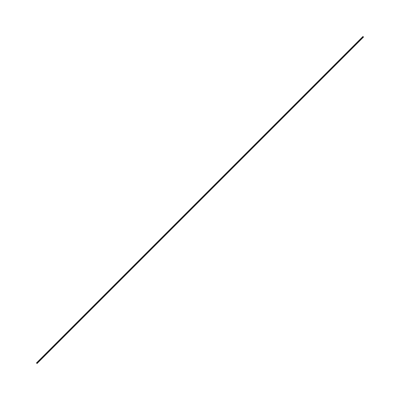

```mathematica
Graphics[Line[{{0,0},{1,1}}]]
```

Trikotnik[{0,0},{5,1},{7,4}]

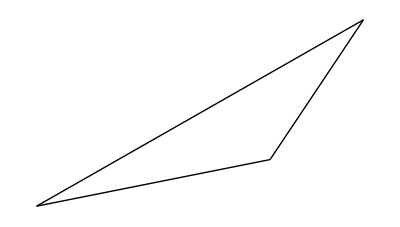

```mathematica
Trikotnik[{0,0}, {5,1}, {7,4}]
Graphics[{Line[{{0,0}, {5,1}}], Line[{{5,1}, {7,4}}], Line[{{7,4},{0,0}}]}]
```

```mathematica
SlikaStranic[Trikotnik[AA_,BB_,CC_]]:=
Graphics[{Line[{AA,BB}], Line[{BB,CC}], Line[{CC,AA}]}]
```

```mathematica
SlikaStranic[T]
```

-Graphics-

```mathematica
NarisiTrikotnik[t_Trikotnik]:= {SlikaOglisc[t], SlikaStranic[t]}
NarisiTrikotnik[T]
```

{-Graphics-,-Graphics-}